```mathematica
fourierFunk[x_,a_,b_]:=a Cos[x]+b Sin[x];
getCoef[f_,n_,l_]:=Module[{ak,bk},
ak=Table[NIntegrate[f[x]Cos[k Pi/l x],{x,-l,l}],{k,0,n-1}]/l;
bk=Table[NIntegrate[f[x]Sin[k Pi/l x],{x,-l,l}],{k,0,n-1}]/l;
bk[[1]]=0;
ak[[1]]/=2;
{ak,bk}
]
approximation[f_,l_,n_]:=Module[{coef,ak,bk,g},
coef=Quiet@getCoef[f,l,n];
ak=coef[[1]];
bk=coef[[2]];
g[x_]:=Total@Table[fourierFunk[x (Pi(i-1))/l,ak[[i]],bk[[i]]],{i,n}];
g
]
showResults[f_,l_]:=Module[{result},
result=approximation[f,l,10];
Show[
Plot[f[x],{x,-l,l}],
Plot[result[x],{x,-l,l},PlotStyle->Orange]
]
]
```

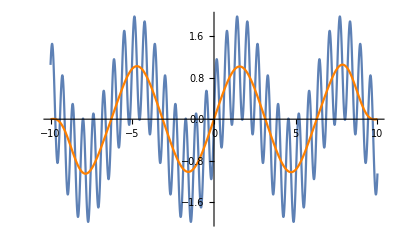

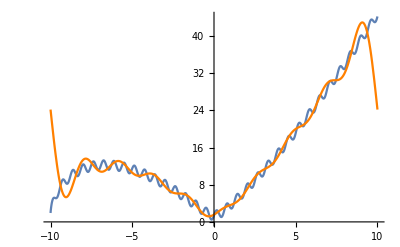

```mathematica
f1[x_]:=Sin[x]+Sin[10x];
f2[x_]:=Sqrt[x^3+10 x^2+2]+Sin[10x]
showResults[f1,10]
showResults[f2,10]
```